```mathematica
gr8=Parallelize[Select[Map[Graph,ReadPlantri["D:\\cygwin64\\home\\alfre\\plantri8.txt"]],ChromaticPolynomial[#,4]==24&]];Length[gr8]
```

7

```mathematica
Table[ChromaticPolynomial[g,x],{g,gr8}]
```

{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8}

```mathematica
Table[FactorTerms[Total[Table[Abs[StirlingS1[4,4-k]]*(x-3)^(n-k),{k,0,3}]]],{n,3,20}]
```

{2 x-3 x^2+x^3,-6 x+11 x^2-6 x^3+x^4,18 x-39 x^2+29 x^3-9 x^4+x^5,-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9,-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,13122 x-54675 x^2+99873 x^3-105948 x^4+72576 x^5-33642 x^6+10710 x^7-2316 x^8+326 x^9-27 x^10+x^11,-39366 x+177147 x^2-354294 x^3+417717 x^4-323676 x^5+173502 x^6-65772 x^7+17658 x^8-3294 x^9+407 x^10-30 x^11+x^12,118098 x-570807 x^2+1240029 x^3-1607445 x^4+1388745 x^5-844182 x^6+370818 x^7-118746 x^8+27540 x^9-4515 x^10+497 x^11-33 x^12+x^13,-354294 x+1830519 x^2-4290894 x^3+6062364 x^4-5773680 x^5+3921291 x^6-1956636 x^7+727056 x^8-201366 x^9+41085 x^10-6006 x^11+596 x^12-36 x^13+x^14,1062882 x-5845851 x^2+14703201 x^3-22477986 x^4+23383404 x^5-17537553 x^6+9791199 x^7-4137804 x^8+1331154 x^9-324621 x^10+59103 x^11-7794 x^12+704 x^13-39 x^14+x^15,-3188646 x+18600435 x^2-49955454 x^3+82137159 x^4-92628198 x^5+75996063 x^6-46911150 x^7+22204611 x^8-8131266 x^9+2305017 x^10-501930 x^11+82485 x^12-9906 x^13+821 x^14-42 x^15+x^16,9565938 x-58989951 x^2+168466797 x^3-296366931 x^4+360021753 x^5-320616387 x^6+216729513 x^7-113524983 x^8+46598409 x^9-15046317 x^10+3810807 x^11-749385 x^12+112203 x^13-12369 x^14+947 x^15-45 x^16+x^17,-28697814 x+186535791 x^2-564390342 x^3+1057567590 x^4-1376432190 x^5+1321870914 x^6-970804926 x^7+557304462 x^8-253320210 x^9+91737360 x^10-26478738 x^11+6058962 x^12-1085994 x^13+149310 x^14-15210 x^15+1082 x^16-48 x^17+x^18,86093442 x-588305187 x^2+1879706817 x^3-3737093112 x^4+5186864160 x^5-5342044932 x^6+4234285692 x^7-2642718312 x^8+1317265092 x^9-528532290 x^10+171173574 x^11-44655624 x^12+9316944 x^13-1533924 x^14+194940 x^15-18456 x^16+1226 x^17-51 x^18+x^19,-258280326 x+1851009003 x^2-6227425638 x^3+13090986153 x^4-19297685592 x^5+21212998956 x^6-18044902008 x^7+12162440628 x^8-6594513588 x^9+2902861962 x^10-1042053012 x^11+305140446 x^12-72606456 x^13+13918716 x^14-2118744 x^15+250308 x^16-22134 x^17+1379 x^18-54 x^19+x^20}

```mathematica
With[{colors=5},
Table[FactorTerms[Total[Table[Abs[StirlingS1[colors,colors-k]]*(x-(colors-1))^(n-k),{k,0,colors-1}]]],{n,3,20}]
]
```

{6+24/(-4+x)+3 x-2 x^2+x^3,-6 x+11 x^2-6 x^3+x^4,24 x-50 x^2+35 x^3-10 x^4+x^5,-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6,384 x-992 x^2+984 x^3-490 x^4+131 x^5-18 x^6+x^7,-1536 x+4352 x^2-4928 x^3+2944 x^4-1014 x^5+203 x^6-22 x^7+x^8,6144 x-18944 x^2+24064 x^3-16704 x^4+7000 x^5-1826 x^6+291 x^7-26 x^8+x^9,-24576 x+81920 x^2-115200 x^3+90880 x^4-44704 x^5+14304 x^6-2990 x^7+395 x^8-30 x^9+x^10,98304 x-352256 x^2+542720 x^3-478720 x^4+269696 x^5-101920 x^6+26264 x^7-4570 x^8+515 x^9-34 x^10+x^11,-393216 x+1507328 x^2-2523136 x^3+2457600 x^4-1557504 x^5+677376 x^6-206976 x^7+44544 x^8-6630 x^9+651 x^10-38 x^11+x^12,1572864 x-6422528 x^2+11599872 x^3-12353536 x^4+8687616 x^5-4267008 x^6+1505280 x^7-385152 x^8+71064 x^9-9234 x^10+803 x^11-42 x^12+x^13,-6291456 x+27262976 x^2-52822016 x^3+61014016 x^4-47104000 x^5+25755648 x^6-10288128 x^7+3045888 x^8-669408 x^9+108000 x^10-12446 x^11+971 x^12-46 x^13+x^14,25165824 x-115343360 x^2+238551040 x^3-296878080 x^4+249430016 x^5-150126592 x^6+66908160 x^7-22471680 x^8+5723520 x^9-1101408 x^10+157784 x^11-16330 x^12+1155 x^13-50 x^14+x^15,-100663296 x+486539264 x^2-1069547520 x^3+1426063360 x^4-1294598144 x^5+849936384 x^6-417759232 x^7+156794880 x^8-45365760 x^9+10129152 x^10-1732544 x^11+223104 x^12-20950 x^13+1355 x^14-54 x^15+x^16,402653184 x-2046820352 x^2+4764729344 x^3-6773800960 x^4+6604455936 x^5-4694343680 x^6+2520973312 x^7-1044938752 x^8+338257920 x^9-85882368 x^10+17059328 x^11-2624960 x^12+306904 x^13-26370 x^14+1571 x^15-58 x^16+x^17,-1610612736 x+8589934592 x^2-21105737728 x^3+31859933184 x^4-33191624704 x^5+25381830656 x^6-14778236928 x^7+6700728320 x^8-2397970432 x^9+681787392 x^10-154119680 x^11+27559168 x^12-3852576 x^13+412384 x^14-32654 x^15+1803 x^16-62 x^17+x^18,6442450944 x-35970351104 x^2+93012885504 x^3-148545470464 x^4+164626432000 x^5-134718947328 x^6+84494778368 x^7-41581150208 x^8+16292610048 x^9-5125120000 x^10+1298266112 x^11-264356352 x^12+42969472 x^13-5502112 x^14+543000 x^15-39866 x^16+2051 x^17-66 x^18+x^19,-25769803776 x+150323855360 x^2-408021893120 x^3+687194767360 x^4-807051198464 x^5+703502221312 x^6-472698060800 x^7+250819379200 x^8-106751590400 x^9+36793090048 x^10-10318184448 x^11+2355691520 x^12-436234240 x^13+64977920 x^14-7674112 x^15+702464 x^16-48070 x^17+2315 x^18-70 x^19+x^20}

```mathematica
g6=GenerateAllGraphsOfSize[6];
```

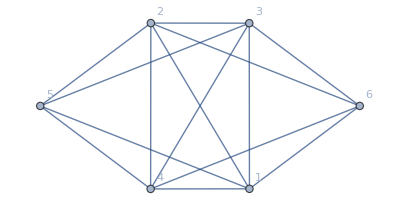
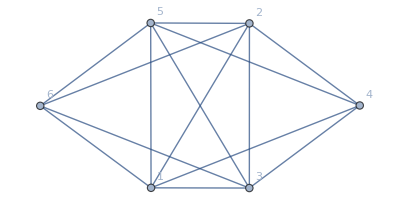
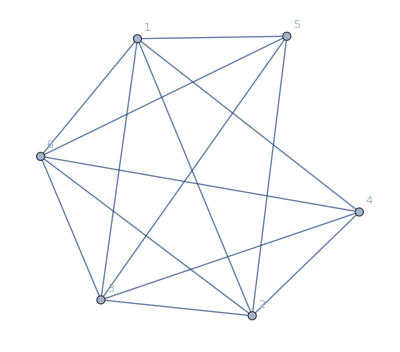
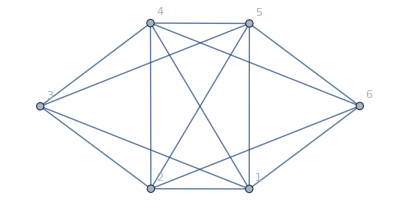
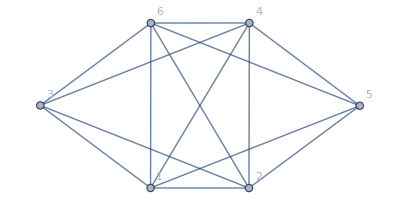
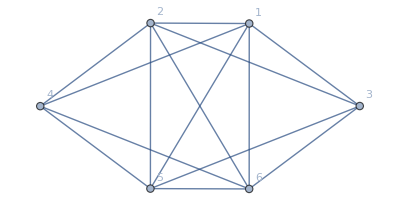
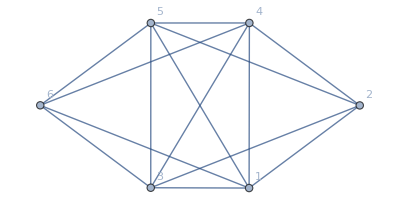
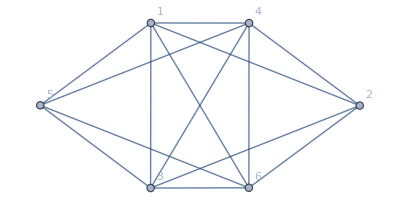

```mathematica
g65=Select[g6,ChromaticPolynomial[#,x]==-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6&]
```

```mathematica
Tally[g65,IsomorphicGraphQ]
```

{{-Graphics-,15}}

```mathematica
ChromaticPolynomial[g6[[1]]]
```

Function[x,-x+5 x^2-10 x^3+10 x^4-5 x^5+x^6]

```mathematica
Table[FindFullFormula[ Graph[g]],{g,g65}]
```

{{v1x2x3x4x5x6,v1x2x3x4x56},{v1x2x3x4x5x6,v1x2x3x46x5},{v1x2x3x4x5x6,v1x2x3x45x6},{v1x2x3x4x5x6,v1x2x36x4x5},{v1x2x3x4x5x6,v1x2x35x4x6},{v1x2x3x4x5x6,v1x2x34x5x6},{v1x2x3x4x5x6,v1x26x3x4x5},{v1x2x3x4x5x6,v1x25x3x4x6},{v1x2x3x4x5x6,v1x24x3x5x6},{v1x2x3x4x5x6,v1x23x4x5x6},{v1x2x3x4x5x6,v16x2x3x4x5},{v1x2x3x4x5x6,v15x2x3x4x6},{v1x2x3x4x5x6,v14x2x3x5x6},{v1x2x3x4x5x6,v13x2x4x5x6},{v1x2x3x4x5x6,v12x3x4x5x6}}

```mathematica
Table[PlanarGraphQ[ Graph[g]],{g,g65}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

## Now with seven

```mathematica
g7=GenerateAllGraphsOfSize[7];
```

```mathematica
g7Bis=Tally[g7,IsomorphicGraphQ]; Length[g7Bis]
```

$Aborted

```mathematica
g75=Select[Map[First,g7Bis],ChromaticPolynomial[#,x]==384 x-992 x^2+984 x^3-490 x^4+131 x^5-18 x^6+x^7&];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Tally[g75,IsomorphicGraphQ]
```

{{-Graphics-,15}}

```mathematica
ChromaticPolynomial[g75[[1]]]
```

Function[x,-x+5 x^2-10 x^3+10 x^4-5 x^5+x^6]

```mathematica
Table[FindFullFormula[ Graph[g]],{g,g75}]
```

{{v1x2x3x4x5x6,v1x2x3x4x56},{v1x2x3x4x5x6,v1x2x3x46x5},{v1x2x3x4x5x6,v1x2x3x45x6},{v1x2x3x4x5x6,v1x2x36x4x5},{v1x2x3x4x5x6,v1x2x35x4x6},{v1x2x3x4x5x6,v1x2x34x5x6},{v1x2x3x4x5x6,v1x26x3x4x5},{v1x2x3x4x5x6,v1x25x3x4x6},{v1x2x3x4x5x6,v1x24x3x5x6},{v1x2x3x4x5x6,v1x23x4x5x6},{v1x2x3x4x5x6,v16x2x3x4x5},{v1x2x3x4x5x6,v15x2x3x4x6},{v1x2x3x4x5x6,v14x2x3x5x6},{v1x2x3x4x5x6,v13x2x4x5x6},{v1x2x3x4x5x6,v12x3x4x5x6}}